```mathematica
LambertW[.0001]
```

0.00009999

```mathematica
2Pi E//N
```

17.0795

```mathematica
Assuming[n>10,Log[10^n/E]-Log[Log[10^n/E]]//FullSimplify]
```

-1+n Log[10]-Log[-1+n Log[10]]

```mathematica
2Pi 10^n/%
```

(2^(1+n) 5^n π)/(-1+n Log[10]-Log[-1+n Log[10]])

```mathematica
2Pi 10^n/(n Log[10])
```

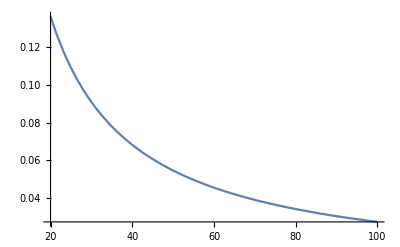

```mathematica
Plot[2Pi/(n Log[10]),{n,20,100}]
```

```mathematica
2Pi/(100 Log[10])//N
```

0.0272875

```mathematica
2Pi/(Log[10^100/E]-Log[Log[10^100/E]])//N
```

0.028072

```mathematica
Clear[l1,l2]
```

```mathematica
l1:=Log[10^100/E]
l2:=Log[l1]
```

```mathematica
N[2Pi/(l1-l2+l2/l1+l2(l2-2)/(2l1^2)),20]
```

0.028069038536932673879

```mathematica
N[2Pi/LambertW[10^100/E],110]
```

0.028069038384289406990319544583825640008454803016284604519236005922493092234907304306033565310925247327193662894

```mathematica
D[2Pi(n-11/8)/LambertW[(n-11/8)/E],n]
```

(2 π)/ProductLog[(-11/8+n)/ⅇ]-(2 π)/(ProductLog[(-11/8+n)/ⅇ] (1+ProductLog[(-11/8+n)/ⅇ]))

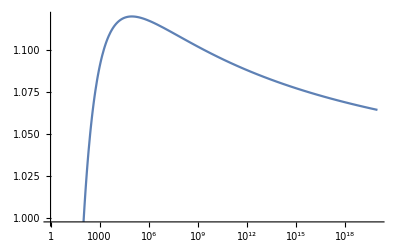

```mathematica
LogLinearPlot[((2 π)/ProductLog[(-11/8+n)/ⅇ]-(2 π)/(ProductLog[(-11/8+n)/ⅇ] (1+ProductLog[(-11/8+n)/ⅇ])))Log[n/E]/(2Pi),{n,1,10^20}]
```